# Notebook for : Gravitational waves from hyperbolic encounters by Capozziello et al

Geoff Cope
University of Utah
October 14th, 2021

## Hyperlink To Paper

```mathematica
Hyperlink["Gravitational waves from hyperbolic encounters by Capozziello et al",
"https://arxiv.org/abs/0801.0122"]
```

[Gravitational waves from hyperbolic encounters by Capozziello et al](https://arxiv.org/abs/0801.0122)

## Utilities

```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 5 Kb

{Utilities`CleanSlate`,DocumentationSearch`,ResourceLocator`,System`,Global`}

```mathematica
Clear[eq2]
eq2 = 
 v == {r'[t] , r[t] ϕ'[t] }
```

v=={r'[t],r[t] ϕ'[t]}

```mathematica
Clear[eq3]
eq3 = 
(1/2)( eq2[[2]]  . eq2[[2]] )   +Φ[r]
```

Φ[r]+1/2 (r'[t]^2+r[t]^2 ϕ'[t]^2)

```mathematica
Clear[eq4]
eq4 = 
L == r[t]^2 ϕ'[t]
```

L==r[t]^2 ϕ'[t]

```mathematica
Flatten[Solve[ eq4 , ϕ'[t]]][[1]]
```

ϕ'[t]→L/r[t]^2

## My Sad Attempt At The Chain Rule ( Ignore this and Redo another day when you have time )

```mathematica
Clear[eq4a]
eq4a = 
u[ϕ] == 1/r[t[ϕ]]
```

u[ϕ]==1/r[t[ϕ]]

```mathematica
Clear[derivativeReplace]
derivativeReplace =  { 
D[ t[ϕ],ϕ ] -> 1/D[ ϕ[t],t ] , 
D[ ϕ[t],t ] -> 1/D[ t[ϕ],ϕ ]
} ;
derivativeReplace  // TableForm
```

t'[ϕ]→1/ϕ'[t]
ϕ'[t]→1/t'[ϕ]

```mathematica
D[ eq4a[[2]],ϕ ] 
 D[ eq4a[[2]],ϕ ]  /. t[ϕ]-> t 
 D[ eq4a[[2]],ϕ ]  /. t[ϕ]-> t /. derivativeReplace 
 D[ eq4a[[2]],ϕ ]  /. t[ϕ]-> t /. derivativeReplace /. Flatten[Solve[ eq4 , ϕ'[t]]][[1]]
 ( D[ eq4a[[2]],ϕ ]  /. t[ϕ]-> t /. derivativeReplace /. Flatten[Solve[ eq4 , ϕ'[t]]][[1]]  ) /. t-> t[ϕ]
```

-(r'[t[ϕ]] t'[ϕ])/r[t[ϕ]]^2

-(r'[t] t'[ϕ])/r[t]^2

-r'[t]/(r[t]^2 ϕ'[t])

-r'[t]/L

-r'[t[ϕ]]/L

```mathematica
Clear[firstDerivative]
firstDerivative = 
D[ eq4a[[1]],ϕ ] == (  D[ eq4a[[2]],ϕ ]  /. t[ϕ]-> t /. derivativeReplace /. Flatten[Solve[ eq4 , ϕ'[t]]][[1]]  )
```

u'[ϕ]==-r'[t]/L

```mathematica
D[ eq4a[[1]] , ϕ ] 
D[eq4a[[2]],ϕ]    /. t[ϕ]-> t /. t'[ϕ] -> 1/ϕ'[t]
( D[eq4a[[2]],ϕ]    /. t[ϕ]-> t /. t'[ϕ] -> 1/ϕ'[t] ) /. Flatten[Solve[ eq4 , ϕ'[t]]][[1]]
```

u'[ϕ]

-r'[t]/(r[t]^2 ϕ'[t])

-r'[t]/L

```mathematica
D[ eq4a ,ϕ ]
```

u'[ϕ]==-(r'[t[ϕ]] t'[ϕ])/r[t[ϕ]]^2

```mathematica
Clear[eq8]
eq8 = 
u''[ϕ] + u[ϕ] == (G M2)/L^2
```

u[ϕ]+u''[ϕ]==(G M2)/L^2

```mathematica
Clear[eq9a]
eq9a = 
Flatten[DSolve[ eq8 , u[ϕ] , ϕ ]][[1]]  /. Rule-> Equal
```

u[ϕ]==(G M2)/L^2+C[1] Cos[ϕ]+C[2] Sin[ϕ]

```mathematica
eq9a[[2]] /. C[1]-> 𝒞 Cos[ϕ0] /. C[2]-> 𝒞 Sin[ϕ0]
```

(G M2)/L^2+𝒞 Cos[ϕ] Cos[ϕ0]+𝒞 Sin[ϕ] Sin[ϕ0]

```mathematica
Clear[eq9]
eq9 = 
u[ϕ] == ( eq9a[[2]] /. C[1]-> 𝒞 Cos[ϕ0] /. C[2]-> 𝒞 Sin[ϕ0] // FullSimplify )
```

u[ϕ]==(G M2)/L^2+𝒞 Cos[ϕ-ϕ0]

```mathematica
Clear[eq9b]
eq9b = { 
μ == (M1 M2)/(M1 + M2), 
M == M1 + M2 
} ;
eq9b // TableForm
```

μ==(M1 M2)/(M1+M2)
M==M1+M2

```mathematica
Clear[eq10]
eq10 = 
eq9 /. M2-> ( M1+M2 )
```

u[ϕ]==(G (M1+M2))/L^2+𝒞 Cos[ϕ-ϕ0]

```mathematica
eq10 /. ϕ-> ϕ[t]
```

u[ϕ[t]]==(G (M1+M2))/L^2+𝒞 Cos[ϕ0-ϕ[t]]

```mathematica
D[ ( eq10 /. ϕ-> ϕ[t] ) , t  ]
```

u'[ϕ[t]] ϕ'[t]==𝒞 Sin[ϕ0-ϕ[t]] ϕ'[t]

```mathematica
Clear[eq11]
eq11 = 
r'[t] == 𝒞 L Sin[ϕ[t]-ϕ0]
```

r'[t]==-L 𝒞 Sin[ϕ0-ϕ[t]]

```mathematica
Clear[eq12]
eq12 = 
𝒞 == v0/(L Sin[ϕ0])
```

𝒞==(v0 Csc[ϕ0])/L

```mathematica
Clear[eq12a]
eq12a = 
L == b v0
```

L==b v0

```mathematica
( eq12a /. Equal-> Rule  )
```

L→b v0

```mathematica
Clear[eq13]
eq13 = 
( eq12 /. ( eq12a /. Equal-> Rule  )  /. Equal-> Rule )
```

𝒞→Csc[ϕ0]/b

```mathematica
Clear[eq14]
eq14 = 
𝒞 == (-G(M1+M2))/(b^2 Cos[ϕ0])
```

𝒞==-(G (M1+M2) Sec[ϕ0])/b^2

```mathematica
Clear[eq15] (* I don't think this is right *) 
eq15 = 
Tan[ϕ0] == (- b v0^2)/(G(M1+M2))
```

Tan[ϕ0]==-(b v0^2)/(G (M1+M2))

```mathematica
Clear[eq15a]
eq15a = 
Flatten[Solve[ eq15 , ϕ0]][[1]] /. C[1]-> 0
```

ϕ0→-ArcTan[(b v0^2)/(G (M1+M2))]

```mathematica
Clear[eq16]
eq16 = 
r[t] == (b Sin[ϕ0])/(Cos[ϕ[t]-ϕ0]-Cos[ϕ0])
```

r[t]==(b Sin[ϕ0])/(-Cos[ϕ0]+Cos[ϕ0-ϕ[t]])

```mathematica
eq16
```

r==(b Sin[ϕ0])/(Cos[ϕ-ϕ0]-Cos[ϕ0])

## Quadrupole Mass Tensor (Derive This Sometime Instead of Typing It In)

```mathematica
Clear[D11]
D11 = μ r[t]^2(3 Cos[ϕ[t]]^2-1 )
```

μ (-1+3 Cos[ϕ[t]]^2) r[t]^2

```mathematica
Clear[D22]
D22 = μ r[t]^2( 3 Sin[ϕ[t]]^2-1 )
```

μ r[t]^2 (-1+3 Sin[ϕ[t]]^2)

```mathematica
Clear[D12]
D12 = 
3 μ r[t]^2 Sin[ϕ[t]] Cos[ϕ[t]]
```

3 μ Cos[ϕ[t]] r[t]^2 Sin[ϕ[t]]

```mathematica
Clear[D21]
D21 = 
3 μ r[t]^2 Sin[ϕ[t]] Cos[ϕ[t]]
```

3 μ Cos[ϕ[t]] r[t]^2 Sin[ϕ[t]]

```mathematica
Clear[D33]
D33 = 
-μ r[t]^2
```

-μ r[t]^2

```mathematica
Clear[𝒟]
𝒟 = 
({{D11, D12, 0}, {D21, D22, 0}, {0, 0, D33}}) ;
𝒟  // MatrixForm
```

(μ (-1+3 Cos[ϕ[t]]^2) r[t]^2 | 3 μ Cos[ϕ[t]] r[t]^2 Sin[ϕ[t]] | 0
3 μ Cos[ϕ[t]] r[t]^2 Sin[ϕ[t]] | μ r[t]^2 (-1+3 Sin[ϕ[t]]^2) | 0
0 | 0 | -μ r[t]^2)

## Expressions To Simplify Derivatives (Change These - Use Eq 12 & 13)

```mathematica
Clear[simplifying]
simplifying = { 
Flatten[Solve[ eq4 , ϕ'[t]]][[1]] , 
( eq11  /. Equal-> Rule )   , 
eq15a , 
eq16 /. Equal-> Rule 
} ;
simplifying   // TableForm
```

ϕ'[t]→L/r[t]^2
r'[t]→-L 𝒞 Sin[ϕ0-ϕ[t]]
ϕ0→-ArcTan[(b v0^2)/(G (M1+M2))]
r[t]→(b Sin[ϕ0])/(-Cos[ϕ0]+Cos[ϕ0-ϕ[t]])

```mathematica
Clear[rDotPhiDot]
rDotPhiDot = { 
Flatten[Solve[ eq4 , ϕ'[t]]][[1]] , 
( eq11  /. Equal-> Rule )
} ;
rDotPhiDot  // TableForm
```

ϕ'[t]→L/r[t]^2
r'[t]→-L 𝒞 Sin[ϕ0-ϕ[t]]

## First, Second, and Third Derivatives of Quadrupole Mass Tensor

```mathematica
Clear[firstD]
firstD = 
D[ 𝒟 , t ]  /. rDotPhiDot // Expand // Simplify   ;
firstD// MatrixForm
```

(L μ (-𝒞 (1+3 Cos[2 ϕ[t]]) r[t] Sin[ϕ0-ϕ[t]]-3 Sin[2 ϕ[t]]) | 3 L μ (Cos[2 ϕ[t]]-𝒞 r[t] Sin[ϕ0-ϕ[t]] Sin[2 ϕ[t]]) | 0
3 L μ (Cos[2 ϕ[t]]-𝒞 r[t] Sin[ϕ0-ϕ[t]] Sin[2 ϕ[t]]) | L μ (𝒞 (-1+3 Cos[2 ϕ[t]]) r[t] Sin[ϕ0-ϕ[t]]+3 Sin[2 ϕ[t]]) | 0
0 | 0 | 2 L 𝒞 μ r[t] Sin[ϕ0-ϕ[t]])

```mathematica
Clear[secondD]
secondD = 
( D[ firstD , t ] /. rDotPhiDot // Expand // Simplify   // Expand // Apart // Expand ) /. simplifying[[4]]  ;
secondD // MatrixForm
```

(-(L^2 𝒞 μ (-Cos[ϕ0]+Cos[ϕ0-ϕ[t]]) Cos[ϕ[t]] Cot[ϕ0])/(2 b)+(9 L^2 𝒞 μ Cos[ϕ0-3 ϕ[t]] (-Cos[ϕ0]+Cos[ϕ0-ϕ[t]]) Csc[ϕ0])/(2 b)-(6 L^2 μ (-Cos[ϕ0]+Cos[ϕ0-ϕ[t]])^2 Cos[2 ϕ[t]] Csc[ϕ0]^2)/b^2+L^2 𝒞^2 μ Sin[ϕ0-ϕ[t]]^2+3 L^2 𝒞^2 μ Cos[2 ϕ[t]] Sin[ϕ0-ϕ[t]]^2+(5 L^2 𝒞 μ (-Cos[ϕ0]+Cos[ϕ0-ϕ[t]]) Sin[ϕ[t]])/(2 b) | -(9 L^2 𝒞 μ (-Cos[ϕ0]+Cos[ϕ0-ϕ[t]]) Csc[ϕ0] Sin[ϕ0-3 ϕ[t]])/(2 b)-(6 L^2 μ (-Cos[ϕ0]+Cos[ϕ0-ϕ[t]])^2 Csc[ϕ0]^2 Sin[2 ϕ[t]])/b^2+3 L^2 𝒞^2 μ Sin[ϕ0-ϕ[t]]^2 Sin[2 ϕ[t]]-(3 L^2 𝒞 μ (-Cos[ϕ0]+Cos[ϕ0-ϕ[t]]) Csc[ϕ0] Sin[ϕ0+ϕ[t]])/(2 b) | 0
-(9 L^2 𝒞 μ (-Cos[ϕ0]+Cos[ϕ0-ϕ[t]]) Csc[ϕ0] Sin[ϕ0-3 ϕ[t]])/(2 b)-(6 L^2 μ (-Cos[ϕ0]+Cos[ϕ0-ϕ[t]])^2 Csc[ϕ0]^2 Sin[2 ϕ[t]])/b^2+3 L^2 𝒞^2 μ Sin[ϕ0-ϕ[t]]^2 Sin[2 ϕ[t]]-(3 L^2 𝒞 μ (-Cos[ϕ0]+Cos[ϕ0-ϕ[t]]) Csc[ϕ0] Sin[ϕ0+ϕ[t]])/(2 b) | (5 L^2 𝒞 μ (-Cos[ϕ0]+Cos[ϕ0-ϕ[t]]) Cos[ϕ[t]] Cot[ϕ0])/(2 b)-(9 L^2 𝒞 μ Cos[ϕ0-3 ϕ[t]] (-Cos[ϕ0]+Cos[ϕ0-ϕ[t]]) Csc[ϕ0])/(2 b)+(6 L^2 μ (-Cos[ϕ0]+Cos[ϕ0-ϕ[t]])^2 Cos[2 ϕ[t]] Csc[ϕ0]^2)/b^2+L^2 𝒞^2 μ Sin[ϕ0-ϕ[t]]^2-3 L^2 𝒞^2 μ Cos[2 ϕ[t]] Sin[ϕ0-ϕ[t]]^2-(L^2 𝒞 μ (-Cos[ϕ0]+Cos[ϕ0-ϕ[t]]) Sin[ϕ[t]])/(2 b) | 0
0 | 0 | -(2 L^2 𝒞 μ Cos[ϕ0-ϕ[t]] (-Cos[ϕ0]+Cos[ϕ0-ϕ[t]]) Csc[ϕ0])/b-2 L^2 𝒞^2 μ Sin[ϕ0-ϕ[t]]^2)

```mathematica
simplifying
```

{ϕ'[t]→L/r[t]^2,r'[t]→-L 𝒞 Sin[ϕ0-ϕ[t]],ϕ0→-ArcTan[(b v0^2)/(G (M1+M2))],r[t]→(b Sin[ϕ0])/(-Cos[ϕ0]+Cos[ϕ0-ϕ[t]])}

```mathematica
Clear[thirdD]
thirdD = 
( ( D[ secondD , t ]   /. rDotPhiDot // Simplify  ) /. simplifying[[4]] /. eq13  ) // Expand // Simplify  ;
thirdD // MatrixForm
```

((L^3 μ Csc[ϕ0]^4 Sin[ϕ0-ϕ[t]/2]^2 Sin[ϕ[t]/2]^2 (9 Sin[2 ϕ0-3 ϕ[t]]-12 Sin[2 (ϕ0-ϕ[t])]-2 Sin[2 ϕ0-ϕ[t]]-13 Sin[ϕ[t]]+24 Sin[2 ϕ[t]]-9 Sin[3 ϕ[t]]+12 Sin[2 (ϕ0+ϕ[t])]-15 Sin[2 ϕ0+ϕ[t]]))/b^4 | (6 L^3 μ Csc[ϕ0]^4 Sin[ϕ0-ϕ[t]/2]^2 Sin[ϕ[t]/2]^3 (3 Sin[2 ϕ0-(5 ϕ[t])/2]-Sin[2 ϕ0-(3 ϕ[t])/2]-Sin[2 ϕ0-ϕ[t]/2]+5 Sin[(3 ϕ[t])/2]-3 Sin[(5 ϕ[t])/2]-Sin[1/2 (4 ϕ0+ϕ[t])]+4 Sin[2 ϕ0+(3 ϕ[t])/2]))/b^4 | 0
(6 L^3 μ Csc[ϕ0]^4 Sin[ϕ0-ϕ[t]/2]^2 Sin[ϕ[t]/2]^3 (3 Sin[2 ϕ0-(5 ϕ[t])/2]-Sin[2 ϕ0-(3 ϕ[t])/2]-Sin[2 ϕ0-ϕ[t]/2]+5 Sin[(3 ϕ[t])/2]-3 Sin[(5 ϕ[t])/2]-Sin[1/2 (4 ϕ0+ϕ[t])]+4 Sin[2 ϕ0+(3 ϕ[t])/2]))/b^4 | (L^3 μ Csc[ϕ0]^4 Sin[ϕ0-ϕ[t]/2]^2 Sin[ϕ[t]/2]^2 (-9 Sin[2 ϕ0-3 ϕ[t]]+12 Sin[2 (ϕ0-ϕ[t])]-2 Sin[2 ϕ0-ϕ[t]]+17 Sin[ϕ[t]]-24 Sin[2 ϕ[t]]+9 Sin[3 ϕ[t]]-12 Sin[2 (ϕ0+ϕ[t])]+15 Sin[2 ϕ0+ϕ[t]]))/b^4 | 0
0 | 0 | (8 L^3 μ Cot[ϕ0] Csc[ϕ0]^3 Sin[ϕ0-ϕ[t]] Sin[ϕ0-ϕ[t]/2]^2 Sin[ϕ[t]/2]^2)/b^4)

## Simplification To Get Equation 21

```mathematica
Clear[eq21a]
eq21a = 
Sum[ thirdD[[i,j]] thirdD[[i,j]] , {i,1,3},{j,1,3} ] // Expand // Simplify
```

(192 L^6 μ^2 (25+12 Cos[2 ϕ0]+11 Cos[2 (ϕ0-ϕ[t])]-24 Cos[2 ϕ0-ϕ[t]]-24 Cos[ϕ[t]]) Cot[ϕ0]^2 Csc[ϕ0]^6 Sin[ϕ0-ϕ[t]/2]^4 Sin[ϕ[t]/2]^4)/b^8

```mathematica
(*
To see that this expresion is equivalent to the paper rewrite this way...
*)
```

```mathematica
(1/6)*( eq21a[[1;;4]] )
```

(32 L^6 μ^2)/b^8

```mathematica
Expand[6*eq21a[[5]]]
```

150+72 Cos[2 ϕ0]+66 Cos[2 (ϕ0-ϕ[t])]-144 Cos[2 ϕ0-ϕ[t]]-144 Cos[ϕ[t]]

```mathematica
eq21a[[6;;9]]
```

Cot[ϕ0]^2 Csc[ϕ0]^6 Sin[ϕ0-ϕ[t]/2]^4 Sin[ϕ[t]/2]^4

```mathematica
Clear[eq20]
eq20 = 
(1/6)*( eq21a[[1;;4]] )  f[ϕ,ϕ0]
```

(32 L^6 μ^2 f[ϕ,ϕ0])/b^8

```mathematica
Clear[eq21b]
eq21b = 
( (1/6)*( eq21a[[1;;4]] )  ) * ( Expand[6*eq21a[[5]]] ) *eq21a[[6;;9]]
```

(32 L^6 μ^2 (150+72 Cos[2 ϕ0]+66 Cos[2 (ϕ0-ϕ[t])]-144 Cos[2 ϕ0-ϕ[t]]-144 Cos[ϕ[t]]) Cot[ϕ0]^2 Csc[ϕ0]^6 Sin[ϕ0-ϕ[t]/2]^4 Sin[ϕ[t]/2]^4)/b^8

```mathematica
Clear[eq21]
eq21 = 
f[ϕ,ϕ0]== eq21a[[6;;9]]  * ( Expand[6*eq21a[[5]]] )
```

f[ϕ,ϕ0]==(150+72 Cos[2 ϕ0]+66 Cos[2 (ϕ0-ϕ[t])]-144 Cos[2 ϕ0-ϕ[t]]-144 Cos[ϕ[t]]) Cot[ϕ0]^2 Csc[ϕ0]^6 Sin[ϕ0-ϕ[t]/2]^4 Sin[ϕ[t]/2]^4

```mathematica
Clear[eq22]
eq22 = 
ℰ'[t] == (-G/(45 c^5)) eq20
```

ℰ'[t]==-(32 G L^6 μ^2 f[ϕ,ϕ0])/(45 b^8 c^5)

```mathematica
eq12a /. Equal-> Rule
```

L→b v0

```mathematica
Clear[eq23]
eq23 = 
eq22  /. ( eq12a /. Equal-> Rule  )
```

ℰ'[t]==-(32 G v0^6 μ^2 f[ϕ,ϕ0])/(45 b^2 c^5)

```mathematica
eq9b[[1]]
eq9b[[1]] /. M1-> m  /. M2-> m 
( ( eq9b[[1]] /. M1-> m  /. M2-> m  ) /. Equal-> Rule  )
```

μ==(M1 M2)/(M1+M2)

μ==m/2

μ→m/2

```mathematica
eq23 /. ( ( eq9b[[1]] /. M1-> m  /. M2-> m  ) /. Equal-> Rule  )
```

ℰ'[t]==-(8 G m^2 v0^6 f[ϕ,ϕ0])/(45 b^2 c^5)

```mathematica
Flatten[Solve[ Subscript[r, s]== (2 G m)/c^2, G]][[1]]
```

G→(c^2 r_s)/(2 m)

```mathematica
Clear[eq24]
eq24 = 
eq23 /. ( ( eq9b[[1]] /. M1-> m  /. M2-> m  ) /. Equal-> Rule  )   /. Flatten[Solve[ Subscript[r, s]==(2 G m)/c^2 , G]][[1]]
```

ℰ'[t]==-(4 m v0^6 f[ϕ,ϕ0] r_s)/(45 b^2 c^3)

```mathematica
eq4 
eq12a
eq4 [[2]]== eq12a[[2]]
Flatten[Solve[ eq4 [[2]]== eq12a[[2]] , ϕ'[t]]][[1]]
```

L==r[t]^2 ϕ'[t]

L==b v0

r[t]^2 ϕ'[t]==b v0

ϕ'[t]→(b v0)/r[t]^2

```mathematica
(* 
Hard to show using the chain rule symbolically but....
*)
dℰ ==  (dℰ/dt)(dt/dϕ) dϕ ==  (dℰ/dt)(1/ϕ'[t]) dϕ  ==  (dℰ/dt)( (b v0)/r[t]^2) dϕ
```

```mathematica
( eq16 /. Equal-> Rule  )
```

r[t]→(b Sin[ϕ0])/(-Cos[ϕ0]+Cos[ϕ0-ϕ[t]])

```mathematica
eq24
(-1)*eq24[[2]] *(1/ϕ'[t] /. Flatten[Solve[ eq4 [[2]]== eq12a[[2]] , ϕ'[t]]][[1]] ) 

Clear[eq26]
eq26 = 
(-1)*eq24[[2]] *(1/ϕ'[t] /. Flatten[Solve[ eq4 [[2]]== eq12a[[2]] , ϕ'[t]]][[1]] )  /. ( eq16 /. Equal-> Rule  )
```

ℰ'[t]==-(4 m v0^6 f[ϕ,ϕ0] r_s)/(45 b^2 c^3)

(4 m v0^5 f[ϕ,ϕ0] r[t]^2 r_s)/(45 b^3 c^3)

(4 m v0^5 f[ϕ,ϕ0] Sin[ϕ0]^2 r_s)/(45 b c^3 (-Cos[ϕ0]+Cos[ϕ0-ϕ[t]])^2)

```mathematica
eq26 
(  eq21  /. Equal-> Rule )
( eq26 /.(  eq21  /. Equal-> Rule )  )
```

(4 m v0^5 f[ϕ,ϕ0] Sin[ϕ0]^2 r_s)/(45 b c^3 (-Cos[ϕ0]+Cos[ϕ0-ϕ[t]])^2)

f[ϕ,ϕ0]→(150+72 Cos[2 ϕ0]+66 Cos[2 (ϕ0-ϕ[t])]-144 Cos[2 ϕ0-ϕ[t]]-144 Cos[ϕ[t]]) Cot[ϕ0]^2 Csc[ϕ0]^6 Sin[ϕ0-ϕ[t]/2]^4 Sin[ϕ[t]/2]^4

(4 m v0^5 (150+72 Cos[2 ϕ0]+66 Cos[2 (ϕ0-ϕ[t])]-144 Cos[2 ϕ0-ϕ[t]]-144 Cos[ϕ[t]]) Cot[ϕ0]^2 Csc[ϕ0]^4 Sin[ϕ0-ϕ[t]/2]^4 Sin[ϕ[t]/2]^4 r_s)/(45 b c^3 (-Cos[ϕ0]+Cos[ϕ0-ϕ[t]])^2)

```mathematica
Clear[eq27a]
eq27a = 
Integrate[ ( eq26 /.(  eq21  /. Equal-> Rule )  )  , {ϕ[t],ϕ1,ϕ2} ]
```

1/(1440 b c^3)m v0^5 Cot[ϕ0]^2 Csc[ϕ0]^4 (-2628 ϕ1+2628 ϕ2-2328 (ϕ1-ϕ2) Cos[2 ϕ0]-144 (ϕ1-ϕ2) Cos[4 ϕ0]-184 Sin[2 ϕ0-3 ϕ1]-184 Sin[4 ϕ0-3 ϕ1]+426 Sin[4 ϕ0-2 ϕ1]+1140 Sin[2 (ϕ0-ϕ1)]+33 Sin[4 (ϕ0-ϕ1)]-3480 Sin[2 ϕ0-ϕ1]-576 Sin[4 ϕ0-ϕ1]+3480 Sin[ϕ1]-426 Sin[2 ϕ1]+576 Sin[2 ϕ0+ϕ1]+184 Sin[2 ϕ0-3 ϕ2]+184 Sin[4 ϕ0-3 ϕ2]-426 Sin[4 ϕ0-2 ϕ2]-1140 Sin[2 (ϕ0-ϕ2)]-33 Sin[4 (ϕ0-ϕ2)]+3480 Sin[2 ϕ0-ϕ2]+576 Sin[4 ϕ0-ϕ2]-3480 Sin[ϕ2]+426 Sin[2 ϕ2]-576 Sin[2 ϕ0+ϕ2]) r_s

```mathematica
Clear[eq27b] (* I think this looks right *) 
eq27b = 
eq27a /. ϕ1-> 0  /. ϕ2-> 2ϕ0 // Simplify
```

(m v0^5 Cot[ϕ0]^2 Csc[ϕ0]^4 (2628 ϕ0+2328 ϕ0 Cos[2 ϕ0]+144 ϕ0 Cos[4 ϕ0]-1948 Sin[2 ϕ0]-301 Sin[4 ϕ0]) r_s)/(720 b c^3)

```mathematica
Clear[eq28](* I think this looks right *)  
eq28 = 
F[b,v0] == ( (c^3/(v0^5 Subscript[r, s] m)) eq27b  // Simplify  )
```

F[b,v0]==(Cot[ϕ0]^2 Csc[ϕ0]^4 (2628 ϕ0+2328 ϕ0 Cos[2 ϕ0]+144 ϕ0 Cos[4 ϕ0]-1948 Sin[2 ϕ0]-301 Sin[4 ϕ0]))/(720 b)

```mathematica
Clear[eq29,R]
eq29 = 
((2 G)/(R c^4))*( secondD /. eq13  /. ( eq12a /. Equal-> Rule  ) // Expand  // Simplify   )  ;
eq29 // MatrixForm
```

((G v0^2 μ (4-12 Cos[2 ϕ0]+3 Cos[2 ϕ0-3 ϕ[t]]-6 Cos[2 (ϕ0-ϕ[t])]-2 Cos[2 ϕ0-ϕ[t]]+13 Cos[ϕ[t]]-12 Cos[2 ϕ[t]]+3 Cos[3 ϕ[t]]-6 Cos[2 (ϕ0+ϕ[t])]+15 Cos[2 ϕ0+ϕ[t]]) Csc[ϕ0]^2)/(2 c^4 R) | (6 G v0^2 μ Csc[ϕ0]^2 Sin[ϕ[t]/2]^2 (-Sin[2 ϕ0]+Sin[2 (ϕ0-ϕ[t])]+2 Sin[ϕ[t]]-Sin[2 ϕ[t]]+2 Sin[2 ϕ0+ϕ[t]]))/(c^4 R) | 0
(6 G v0^2 μ Csc[ϕ0]^2 Sin[ϕ[t]/2]^2 (-Sin[2 ϕ0]+Sin[2 (ϕ0-ϕ[t])]+2 Sin[ϕ[t]]-Sin[2 ϕ[t]]+2 Sin[2 ϕ0+ϕ[t]]))/(c^4 R) | (G v0^2 μ (4+12 Cos[2 ϕ0]-3 Cos[2 ϕ0-3 ϕ[t]]+6 Cos[2 (ϕ0-ϕ[t])]-2 Cos[2 ϕ0-ϕ[t]]-17 Cos[ϕ[t]]+12 Cos[2 ϕ[t]]-3 Cos[3 ϕ[t]]+6 Cos[2 (ϕ0+ϕ[t])]-15 Cos[2 ϕ0+ϕ[t]]) Csc[ϕ0]^2)/(2 c^4 R) | 0
0 | 0 | (2 G v0^2 μ (-2+Cos[2 ϕ0-ϕ[t]]+Cos[ϕ[t]]) Csc[ϕ0]^2)/(c^4 R))

```mathematica
Clear[eq30a]
eq30a = 
h11 ==  eq29[[1,1]]
```

h11==1/(2 c^4 R)G v0^2 μ (4-12 Cos[2 ϕ0]+3 Cos[2 ϕ0-3 ϕ[t]]-6 Cos[2 (ϕ0-ϕ[t])]-2 Cos[2 ϕ0-ϕ[t]]+13 Cos[ϕ[t]]-12 Cos[2 ϕ[t]]+3 Cos[3 ϕ[t]]-6 Cos[2 (ϕ0+ϕ[t])]+15 Cos[2 ϕ0+ϕ[t]]) Csc[ϕ0]^2

```mathematica
Clear[eq30b]
eq30b = 
h22 ==  eq29[[2,2]]
```

h22==1/(2 c^4 R)G v0^2 μ (4+12 Cos[2 ϕ0]-3 Cos[2 ϕ0-3 ϕ[t]]+6 Cos[2 (ϕ0-ϕ[t])]-2 Cos[2 ϕ0-ϕ[t]]-17 Cos[ϕ[t]]+12 Cos[2 ϕ[t]]-3 Cos[3 ϕ[t]]+6 Cos[2 (ϕ0+ϕ[t])]-15 Cos[2 ϕ0+ϕ[t]]) Csc[ϕ0]^2

```mathematica
Clear[eq30c]
eq30c = 
h12 == eq29[[1,2]]
```

h12==(6 G v0^2 μ Csc[ϕ0]^2 Sin[ϕ[t]/2]^2 (-Sin[2 ϕ0]+Sin[2 (ϕ0-ϕ[t])]+2 Sin[ϕ[t]]-Sin[2 ϕ[t]]+2 Sin[2 ϕ0+ϕ[t]]))/(c^4 R)

```mathematica
Clear[eq31]
eq31 = 
Sqrt[h11^2+ h22^2+2* h12^2] /. { (eq30a /. Equal-> Rule ) , ( eq30b /. Equal-> Rule ), ( eq30c /. Equal-> Rule )   }   // Expand // Simplify // PowerExpand
```

1/(c^4 R)√2 G v0^2 μ √(212+190 Cos[2 ϕ0]+18 Cos[4 ϕ0]-18 Cos[2 ϕ0-3 ϕ[t]]-18 Cos[4 ϕ0-3 ϕ[t]]+59 Cos[4 ϕ0-2 ϕ[t]]+118 Cos[2 (ϕ0-ϕ[t])]-256 Cos[2 ϕ0-ϕ[t]]-54 Cos[4 ϕ0-ϕ[t]]-256 Cos[ϕ[t]]+59 Cos[2 ϕ[t]]-54 Cos[2 ϕ0+ϕ[t]]) Csc[ϕ0]^2

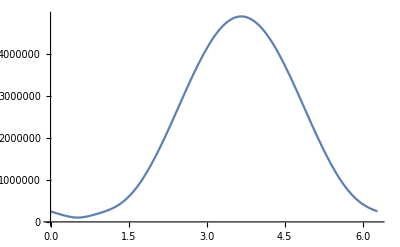

```mathematica
(* Completely made up parameters - Put in real ones when you have time  *) 
Plot[ ( eq31 /. c-> 1 /. G-> 1 /. R-> 1 /. v0-> 200  /. μ-> 0.7 /. ϕ0-> π/6  ) , {ϕ[t],0,2π} ]
```